```mathematica
Import["C:\\Users\\jhenry1\\Documents\\GitHub\\QM_prisoners_dilemma\\Mathematica\\StrategySpaces.wl"]
Import["C:\\Users\\jhenry1\\Documents\\GitHub\\QM_prisoners_dilemma\\Mathematica\\QPD_dynamics.wl"]
Import["C:\\Users\\jhenry1\\Documents\\GitHub\\QM_prisoners_dilemma\\Mathematica\\DiscreteNashEqulibrium.wl"]
```

```mathematica
binaryTetrahedralGroup//Length
```

24

```mathematica
T = DeleteDuplicates[binaryTetrahedralGroup,(#1==#2||#1==-#2)&];
```

```mathematica
Length[T]
```

12

## a=b=0 γ=π/2

```mathematica
strategyGroup = T;
symmetricJ = FullSimplify[(J[0,0,Pi/2]//FullSimplify),Assumptions->0<γ<π/2];
```

```mathematica
finalStates = FullSimplify[Table[play[symmetricJ,strategyGroup[[i]],strategyGroup[[j]]],{i,12},{j,12}]/.Conjugate->MyConj];
```

```mathematica
alicesScores = FullSimplify[(Map[alicesScore,finalStates,{2}]/.Conjugate->MyConj)//Simplify];
bobsScores = FullSimplify[(Map[bobsScore,finalStates,{2}]/.Conjugate->MyConj)//Simplify];
```

```mathematica
alicesScores//MatrixForm
bobsScores//MatrixForm
```

(3 | 9/4 | 9/4 | 1 | 9/4 | 9/4 | 0 | 9/4 | 9/4 | 5 | 9/4 | 9/4
9/4 | 9/4 | 3 | 9/4 | 9/4 | 1 | 9/4 | 9/4 | 0 | 9/4 | 9/4 | 5
9/4 | 3 | 9/4 | 9/4 | 1 | 9/4 | 9/4 | 0 | 9/4 | 9/4 | 5 | 9/4
1 | 9/4 | 9/4 | 3 | 9/4 | 9/4 | 5 | 9/4 | 9/4 | 0 | 9/4 | 9/4
9/4 | 9/4 | 1 | 9/4 | 9/4 | 3 | 9/4 | 9/4 | 5 | 9/4 | 9/4 | 0
9/4 | 1 | 9/4 | 9/4 | 3 | 9/4 | 9/4 | 5 | 9/4 | 9/4 | 0 | 9/4
5 | 9/4 | 9/4 | 0 | 9/4 | 9/4 | 1 | 9/4 | 9/4 | 3 | 9/4 | 9/4
9/4 | 9/4 | 5 | 9/4 | 9/4 | 0 | 9/4 | 9/4 | 1 | 9/4 | 9/4 | 3
9/4 | 5 | 9/4 | 9/4 | 0 | 9/4 | 9/4 | 1 | 9/4 | 9/4 | 3 | 9/4
0 | 9/4 | 9/4 | 5 | 9/4 | 9/4 | 3 | 9/4 | 9/4 | 1 | 9/4 | 9/4
9/4 | 9/4 | 0 | 9/4 | 9/4 | 5 | 9/4 | 9/4 | 3 | 9/4 | 9/4 | 1
9/4 | 0 | 9/4 | 9/4 | 5 | 9/4 | 9/4 | 3 | 9/4 | 9/4 | 1 | 9/4)

(3 | 9/4 | 9/4 | 1 | 9/4 | 9/4 | 5 | 9/4 | 9/4 | 0 | 9/4 | 9/4
9/4 | 9/4 | 3 | 9/4 | 9/4 | 1 | 9/4 | 9/4 | 5 | 9/4 | 9/4 | 0
9/4 | 3 | 9/4 | 9/4 | 1 | 9/4 | 9/4 | 5 | 9/4 | 9/4 | 0 | 9/4
1 | 9/4 | 9/4 | 3 | 9/4 | 9/4 | 0 | 9/4 | 9/4 | 5 | 9/4 | 9/4
9/4 | 9/4 | 1 | 9/4 | 9/4 | 3 | 9/4 | 9/4 | 0 | 9/4 | 9/4 | 5
9/4 | 1 | 9/4 | 9/4 | 3 | 9/4 | 9/4 | 0 | 9/4 | 9/4 | 5 | 9/4
0 | 9/4 | 9/4 | 5 | 9/4 | 9/4 | 1 | 9/4 | 9/4 | 3 | 9/4 | 9/4
9/4 | 9/4 | 0 | 9/4 | 9/4 | 5 | 9/4 | 9/4 | 1 | 9/4 | 9/4 | 3
9/4 | 0 | 9/4 | 9/4 | 5 | 9/4 | 9/4 | 1 | 9/4 | 9/4 | 3 | 9/4
5 | 9/4 | 9/4 | 0 | 9/4 | 9/4 | 3 | 9/4 | 9/4 | 1 | 9/4 | 9/4
9/4 | 9/4 | 5 | 9/4 | 9/4 | 0 | 9/4 | 9/4 | 3 | 9/4 | 9/4 | 1
9/4 | 5 | 9/4 | 9/4 | 0 | 9/4 | 9/4 | 3 | 9/4 | 9/4 | 1 | 9/4)

```mathematica
eq = DiscreteNashEquilibria[(alicesScores),(bobsScores),0<γ<Pi/2];
```

```mathematica
simplifiedEQ= (FullSimplify[{#[[1]],#[[2]],Reduce[#[[3]]]},Assumptions->0<γ<π/2]&/@eq);
```

```mathematica
simplifiedEQ
```

{}

## a=b=0

```mathematica
strategyGroup = T
```

{{{1,0},{0,1}},{{1/2+ⅈ/2,1/2+ⅈ/2},{-1/2+ⅈ/2,1/2-ⅈ/2}},{{-1/2+ⅈ/2,1/2+ⅈ/2},{-1/2+ⅈ/2,-1/2-ⅈ/2}},{{ⅈ,0},{0,-ⅈ}},{{-1/2+ⅈ/2,-1/2+ⅈ/2},{1/2+ⅈ/2,-1/2-ⅈ/2}},{{-1/2-ⅈ/2,-1/2+ⅈ/2},{1/2+ⅈ/2,-1/2+ⅈ/2}},{{0,1},{-1,0}},{{-1/2+ⅈ/2,1/2-ⅈ/2},{-1/2-ⅈ/2,-1/2-ⅈ/2}},{{-1/2+ⅈ/2,-1/2-ⅈ/2},{1/2-ⅈ/2,-1/2-ⅈ/2}},{{0,ⅈ},{ⅈ,0}},{{-1/2-ⅈ/2,1/2+ⅈ/2},{-1/2+ⅈ/2,-1/2+ⅈ/2}},{{-1/2-ⅈ/2,1/2-ⅈ/2},{-1/2-ⅈ/2,-1/2+ⅈ/2}}}

```mathematica
symmetricJ = FullSimplify[(J[0,0,γ]//FullSimplify),Assumptions->0<γ<π/2];
```

```mathematica
finalStates = FullSimplify[Table[play[symmetricJ,strategyGroup[[i]],strategyGroup[[j]]],{i,12},{j,12}]/.Conjugate->MyConj];
```

```mathematica
alicesScores = FullSimplify[(Map[alicesScore,finalStates,{2}]/.Conjugate->MyConj)//Simplify];
bobsScores = FullSimplify[(Map[bobsScore,finalStates,{2}]/.Conjugate->MyConj)//Simplify];
```

```mathematica
alicesScores//MatrixForm
```

(3 | -3/8 (-5+Cos[2 γ]) | -3/8 (-5+Cos[2 γ]) | 2+Cos[2 γ] | -3/8 (-5+Cos[2 γ]) | -3/8 (-5+Cos[2 γ]) | 0 | -3/8 (-5+Cos[2 γ]) | -3/8 (-5+Cos[2 γ]) | 5 Sin[γ]^2 | -3/8 (-5+Cos[2 γ]) | -3/8 (-5+Cos[2 γ])
1/8 (25+7 Cos[2 γ]) | 9/4 | 3/8 (5+Cos[2 γ]+4 Sin[γ]) | 1/8 (25+7 Cos[2 γ]) | 9/4 | -3/8 (-7+Cos[2 γ])-2 Sin[γ] | 1/8 (11-7 Cos[2 γ]) | 9/4 | 3/8 (5+Cos[2 γ]-4 Sin[γ]) | 1/8 (11-7 Cos[2 γ]) | 9/4 | -3/8 (-7+Cos[2 γ])+2 Sin[γ]
1/8 (25+7 Cos[2 γ]) | 1/8 (25-7 Cos[2 γ]-8 Sin[γ]) | 9/4 | 1/8 (25+7 Cos[2 γ]) | 1/4 (8 Cos[γ]^2+(1+Sin[γ])^2) | 9/4 | 1/8 (11-7 Cos[2 γ]) | 2 Cos[γ]^2+1/4 (-1+Sin[γ])^2 | 9/4 | 1/8 (11-7 Cos[2 γ]) | 25/8-7/8 Cos[2 γ]+Sin[γ] | 9/4
2+Cos[2 γ] | -3/8 (-5+Cos[2 γ]) | -3/8 (-5+Cos[2 γ]) | 3 | -3/8 (-5+Cos[2 γ]) | -3/8 (-5+Cos[2 γ]) | 5 Sin[γ]^2 | -3/8 (-5+Cos[2 γ]) | -3/8 (-5+Cos[2 γ]) | 0 | -3/8 (-5+Cos[2 γ]) | -3/8 (-5+Cos[2 γ])
1/8 (25+7 Cos[2 γ]) | 9/4 | -3/8 (-7+Cos[2 γ])-2 Sin[γ] | 1/8 (25+7 Cos[2 γ]) | 9/4 | 3/8 (5+Cos[2 γ]+4 Sin[γ]) | 1/8 (11-7 Cos[2 γ]) | 9/4 | -3/8 (-7+Cos[2 γ])+2 Sin[γ] | 1/8 (11-7 Cos[2 γ]) | 9/4 | 3/8 (5+Cos[2 γ]-4 Sin[γ])
1/8 (25+7 Cos[2 γ]) | 1/4 (8 Cos[γ]^2+(1+Sin[γ])^2) | 9/4 | 1/8 (25+7 Cos[2 γ]) | 1/8 (25-7 Cos[2 γ]-8 Sin[γ]) | 9/4 | 1/8 (11-7 Cos[2 γ]) | 25/8-7/8 Cos[2 γ]+Sin[γ] | 9/4 | 1/8 (11-7 Cos[2 γ]) | 2 Cos[γ]^2+1/4 (-1+Sin[γ])^2 | 9/4
5 | 3/8 (7+Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 5 Cos[γ]^2 | 3/8 (7+Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 1 | 3/8 (7+Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 2-Cos[2 γ] | 3/8 (7+Cos[2 γ]) | 3/8 (7+Cos[2 γ])
1/8 (25+7 Cos[2 γ]) | 9/4 | -3/8 (-7+Cos[2 γ])+2 Sin[γ] | 1/8 (25+7 Cos[2 γ]) | 9/4 | 3/8 (5+Cos[2 γ]-4 Sin[γ]) | 1/8 (11-7 Cos[2 γ]) | 9/4 | -3/8 (-7+Cos[2 γ])-2 Sin[γ] | 1/8 (11-7 Cos[2 γ]) | 9/4 | 3/8 (5+Cos[2 γ]+4 Sin[γ])
1/8 (25+7 Cos[2 γ]) | 25/8-7/8 Cos[2 γ]+Sin[γ] | 9/4 | 1/8 (25+7 Cos[2 γ]) | 2 Cos[γ]^2+1/4 (-1+Sin[γ])^2 | 9/4 | 1/8 (11-7 Cos[2 γ]) | 1/4 (8 Cos[γ]^2+(1+Sin[γ])^2) | 9/4 | 1/8 (11-7 Cos[2 γ]) | 1/8 (25-7 Cos[2 γ]-8 Sin[γ]) | 9/4
5 Cos[γ]^2 | 3/8 (7+Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 5 | 3/8 (7+Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 2-Cos[2 γ] | 3/8 (7+Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 1 | 3/8 (7+Cos[2 γ]) | 3/8 (7+Cos[2 γ])
1/8 (25+7 Cos[2 γ]) | 9/4 | 3/8 (5+Cos[2 γ]-4 Sin[γ]) | 1/8 (25+7 Cos[2 γ]) | 9/4 | -3/8 (-7+Cos[2 γ])+2 Sin[γ] | 1/8 (11-7 Cos[2 γ]) | 9/4 | 3/8 (5+Cos[2 γ]+4 Sin[γ]) | 1/8 (11-7 Cos[2 γ]) | 9/4 | -3/8 (-7+Cos[2 γ])-2 Sin[γ]
1/8 (25+7 Cos[2 γ]) | 2 Cos[γ]^2+1/4 (-1+Sin[γ])^2 | 9/4 | 1/8 (25+7 Cos[2 γ]) | 25/8-7/8 Cos[2 γ]+Sin[γ] | 9/4 | 1/8 (11-7 Cos[2 γ]) | 1/8 (25-7 Cos[2 γ]-8 Sin[γ]) | 9/4 | 1/8 (11-7 Cos[2 γ]) | 2 Cos[γ]^2+1/4 (1+Sin[γ])^2 | 9/4)

```mathematica
eq = DiscreteNashEquilibria[(alicesScores),(bobsScores),0<γ<Pi/2];
```

```mathematica
eq//MatrixForm
```

({7,10} | {2-Cos[2 γ],2-Cos[2 γ]} | 0<γ≤2 ArcTan[√(5-2 √6)]
{10,7} | {2-Cos[2 γ],2-Cos[2 γ]} | 0<γ≤2 ArcTan[√(5-2 √6)])

```mathematica
Manipulate[MatrixPlot[alicesScores/.γ->g],{{g,2 ArcTan[√(5-2 √6)]},0,Pi/2}]
```

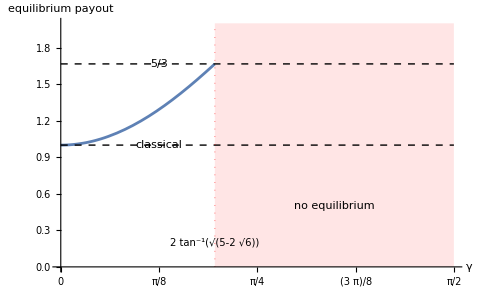

```mathematica
val=2 ArcTan[Sqrt[5-2 Sqrt[6]]];

Plot[Piecewise[{{2-Cos[2 γ],γ<=val}},-1],{γ,0,Pi/2},PlotRange->{0,2},AxesLabel->{"γ","equilibrium payout"},Ticks->{Range[0,Pi/2,Pi/8],Automatic},Prolog->{{Red,Opacity[0.1],Rectangle[{val,0},{Pi/2,2}]}},Epilog->{(*Horizontal Lines*){Dashed,Thin,Line[{{0,1},{Pi/2,1}}]},{Dashed,Thin,Line[{{0,5/3},{Pi/2,5/3}}]},(*Labels*)Text["classical",{Pi/8,1},{0,-1.5}],Text["5/3",{Pi/8,5/3},{0,-1.5}],Text["no equilibrium",{(val+Pi/2)/2,0.5}],(*Vertical Line and Formula Label*){Red,Dotted,Opacity[0.5],Line[{{val,0},{val,2}}]},Text[Style[HoldForm[2 ArcTan[Sqrt[5-2 Sqrt[6]]]],10],{val,0.2},{1.2,0}]}]
```